```mathematica
<<"C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m"
```

## Data input and grooming

Directory where spectra reside. Should be tab separated files, but CSV will probably also work.

```mathematica
DataDir="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS";
```

```mathematica
XPSPath="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

```mathematica
XPSSpecs=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
sheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

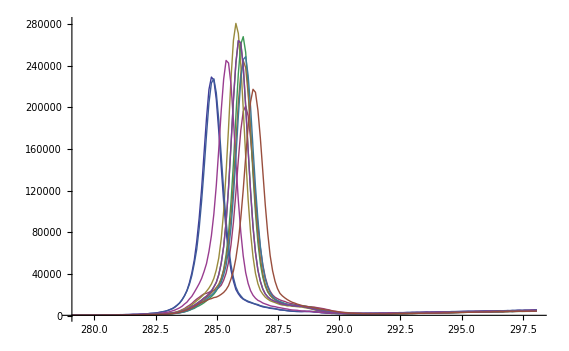

```mathematica
ListLinePlot[XPSSpecs,PlotRange->All]
```

```mathematica
coordlist=CoordInit[XPSSpecs,285,5]
```

{{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}}}

```mathematica
PickGuesses[XPSSpecs,coordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
coordlist
```

{{{285,1000},{280.7,1300.},{290.82,2600.},{290.28,2600.}},{{286.48,4000.},{565/2,1000},{292.01,2600.},{290.84,3000.}},{{285.94,3350.},{565/2,1000},{291.56,2250.},{290.61,2350.}},{{286.48,4100.},{565/2,1000},{291.29,2250.},{290.66,2250.}},{{284.86,3050.},{281.22,1200.},{291.11,2700.},{290.48,2450.}},{{285,1000},{281.49,1500.},{291.15,2250.},{290.43,2450.}},{{285.4,3100.},{565/2,1000},{291.38,2350.},{290.75,2000.}},{{285,1000},{565/2,1000},{291.29,2250.},{290.66,1950.}},{{286.25,6150.},{565/2,1000},{291.29,2300.},{290.43,2550.}},{{285,1000},{565/2,1000},{291.47,2450.},{290.79,2250.}},{{285,1000},{565/2,1000},{291.74,2500.},{290.88,2800.}}}

Pick one spectrum to work with.

```mathematica
data=ChopBoth[XPSSpecs,coordlist][[1]];
```

```mathematica
AllData=ChopBoth[XPSSpecs,coordlist];
```

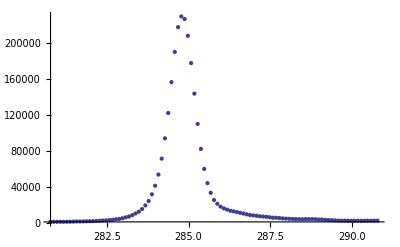

```mathematica
ListPlot[data,PlotRange->All]
```

## Peak fitting XPS data

### Fitting XPS data

#### Simple Fitting

Fit is not very good leaving everything free when the data are far from the origin. Note that the second gaussian is extremely far away from the first, so it has a negligible impact on the fit.

217426. ⅇ^(-2.99934 (-284.808+x)^2)+11142.2 ⅇ^(-5.97738×10^-6 (60.9918+x)^2)

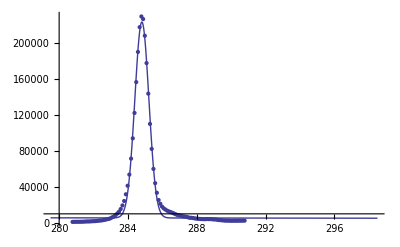

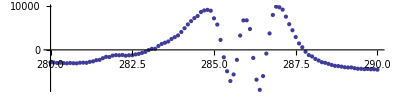

94.5379

```mathematica
nlm=Model[data,2];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"],AspectRatio->0.25,DataRange->{280,290}]
Print[nlm["FitResiduals"]//Total]
```

Centering and normalizing the data does much better. When Mathematica does its optmization routines, it assumes that all parameters are O(1), which means that it has to search a gigantic space. This situation can be somewhat alleviated by picking reasonable guesses (which is performed by Model[] automatically) but it seems that working with the normalized data is the best.

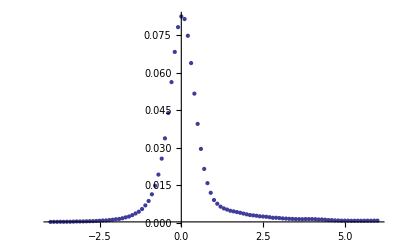

0.000890196 ⅇ^(-0.243997 (-4.93389+x)^2)+0.00479045 ⅇ^(-0.180594 (-0.551007+x)^2)+0.0542504 ⅇ^(-4.93188 (-0.0427552+x)^2)+0.0243921 ⅇ^(-1.6044 (0.0373253+x)^2)

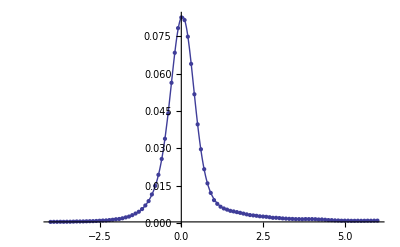

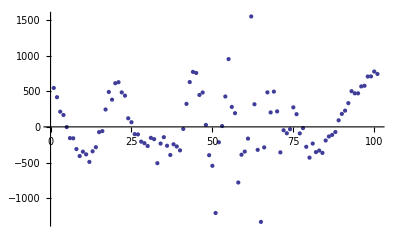

0.00104345

```mathematica
sdata=CenterAndNormalize[data];
ListPlot[sdata,PlotRange->All]
nlm=Model[sdata,4];
nlm[x]
Show[ListPlot[sdata,PlotRange->All],Plot[nlm["Function"][x],{x,-3,3},PlotRange->All]]
ListPlot[nlm["FitResiduals"]*Total[dataᵀ[[2]]]]
Print[(nlm["FitResiduals"]^2//Total)*(60.06/0.1511)]
```

Fit Residuals: 0.00156518

| Weights | Centers
Peak 1
Peak 2
Peak 3
Peak 4 | 0.731514
0.0415963
0.279766
0.0208425 | 0.
0.508252
-0.0800805
4.89113

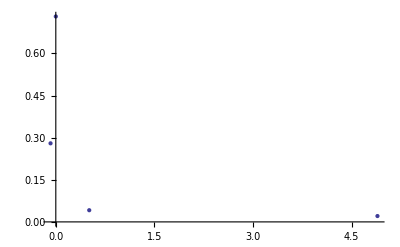

```mathematica
ListPlot[FitSummary[nlm]]
```

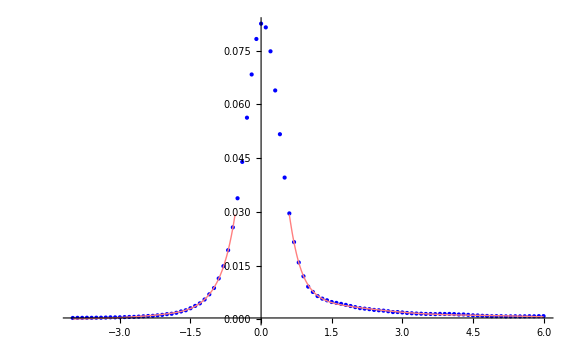
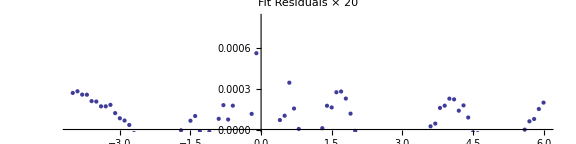

```mathematica
SummaryPlot[sdata,nlm]
```

We can see how the fit improves when adding more gaussians:

```mathematica
Fits=Table[Model[sdata,i],{i,1,6}];
```

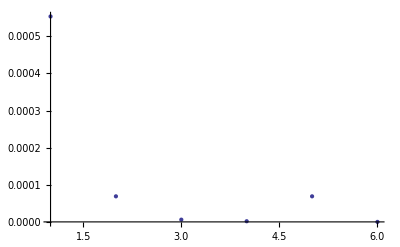

```mathematica
ListPlot[Table[Fits[[i]]["FitResiduals"]^2//Total,{i,1,6}],PlotRange->All]
```

#### Fitting with Voigt profiles

Can also use Voigt profiles. More parameters, trickier to fit. Prone to finding local minima. Not recommended yet.

(221494. 2^(-4.79661 (-284.803+x)^2))/(1-0.48443 (-284.803+x)^2)+(17836. 2^(-0.0489499 (-67.0585+x)^2))/(1-0.0451856 (-67.0585+x)^2)+(948.559 2^(-0.029004 (-20.4369+x)^2))/(1-0.0272774 (-20.4369+x)^2)

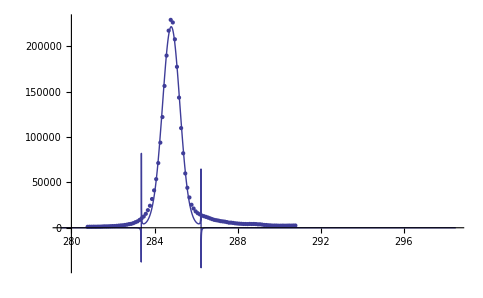

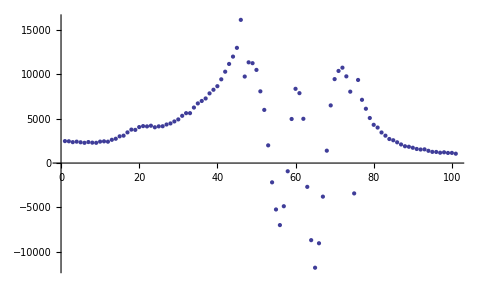

```mathematica
nlm=VoigtModel[data,3];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

#### Fitting by fixing peak positions

Can used knowledge of peak positions with FixedPeaksModel:

279.065 ⅇ^(-0.0000577052 (-288.102+x)^2)+444.521 ⅇ^(-0.0000112515 (-287.002+x)^2)+12323. ⅇ^(-0.128642 (-285.802+x)^2)+213264. ⅇ^(-3.24599 (-284.802+x)^2)

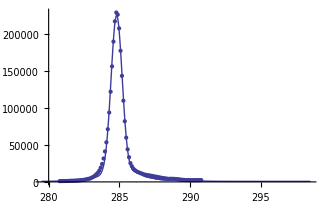

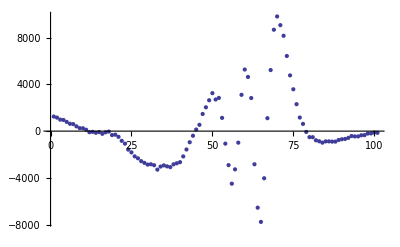

```mathematica
nlm=FixedPeaksModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

#### Fitting with fixed peaks voigt profile

Can used knowledge of peak positions with FixedPeaksModel:

(0.0248885 2^(0.0000582317 (-938.197+x)^2))/(1+0.0000593864 (-938.197+x)^2)

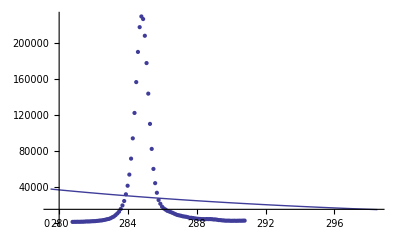

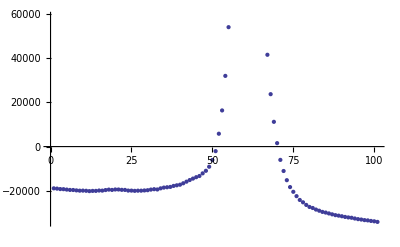

```mathematica
nlm=FixedPeaksVoigtModel[data,{0}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

(1066.75 2^(-60.6086 (-319.713+x)^2))/(1-60.5002 (-319.713+x)^2)+(1.07972×10^6 2^(-0.00330268 (-318.613+x)^2))/(1-0.0000242776 (-318.613+x)^2)+(4.24744×10^6 2^(-0.00451086 (-317.413+x)^2))/(1-0.0044639 (-317.413+x)^2)+(531686. 2^(-0.125433 (-316.413+x)^2))/(1-0.125212 (-316.413+x)^2)

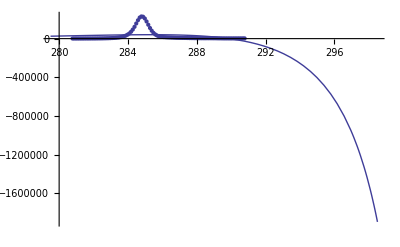

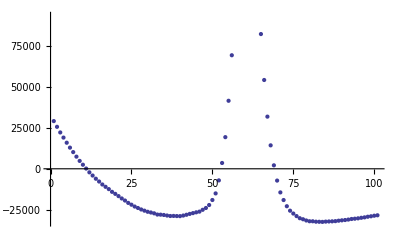

```mathematica
nlm=FixedPeaksVoigtModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

### Fitting example data

Example peak positions for a carbon 1s edge:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

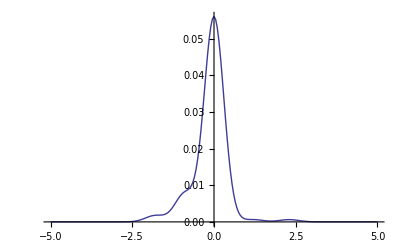

```mathematica
exweights={.10,.21,.57,.06,.06};
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[exweights[[i]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

0.000495078 ⅇ^(-0.577205 (-1.57938+x)^2)+0.0558349 ⅇ^(-5.59817 (0.000301553+x)^2)+0.00759303 ⅇ^(-5.41049 (0.897706+x)^2)+0.00171306 ⅇ^(-5.726 (1.80639+x)^2)+0.2361 ⅇ^(-7.23886 (6.49486+x)^2)

Sum of Squares of Residuals: 1.172628663250082e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3
Peak 4
Peak 5 | 0.790662
0.0239065
1.84883
0.286643
0.140064 | 6.49456
8.07424
0.
5.59715
4.68847

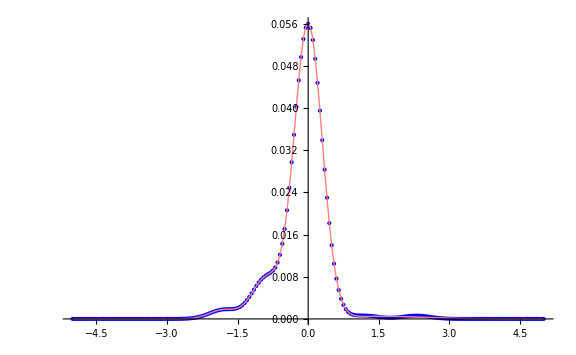
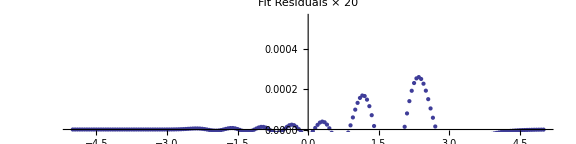

```mathematica
ExCModel=Model[ExampleCData,5]; ExCModel[x]
FitSummary[ExCModel];
SummaryPlot[ExampleCData,ExCModel]
```

```mathematica
FitSummary[data,nlm]
```

Weights | Positions | σs
0.78309 | 0.0427552 | -0.318404
0.0132321 | 0.551007 | -1.66392
0.20082 | -0.0373253 | -0.55825
0.00285812 | 4.93389 | -1.43151

{{0.78309,0.0427552,-0.318404},{0.0132321,0.551007,-1.66392},{0.20082,-0.0373253,-0.55825},{0.00285812,4.93389,-1.43151}}

## Fit all data quickly

### Carbon Edge

```mathematica
RawCData=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
CSheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

```mathematica
Ccoordlist=CoordInit[RawCData,285,5]
```

{{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}}}

```mathematica
PickGuesses[RawCData,Ccoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
CData=ChopBoth[RawCData,Ccoordlist];
```

```mathematica
CenteredCData=CenterAndNormalize/@CData;
```

```mathematica
AllCModels=FixedPeaksModel[#,{-1.8,-0.9,0,1.2,2.3}]&/@CenteredCData;
```

```mathematica
AllCModels=Model[#,3]&/@CenteredCData;
```

```mathematica
fpnlm=FixedPeaksModel[#,{0,-1.8,-0.9,1.2,2.3}]&@CenteredCData[[1]]
```

FittedModel[0.000497546 ⅇ^(-6.23216×10^-8 («1»)^2)+«23» ⅇ^(«1»)+«1»+«1»+0.076214 ⅇ^(«1»)]

Need to get FitSummary working with FixedPeaksModel. If odd number, drop first or last? where is mu? Also need to get weights working properly. Should make fake data from reference and make sure we can fit that.

```mathematica
fpnlm[x]
```

0.000497546 ⅇ^(-6.23216×10^-8 (-4.12188+x)^2)+9.39134×10^-18 ⅇ^(-0.0550997 (-3.02188+x)^2)+544.471 ⅇ^(-65101.9 (-1.82188+x)^2)+0.00448274 ⅇ^(-0.1567 (-0.921879+x)^2)+0.076214 ⅇ^(-3.27781 (-0.0218787+x)^2)

```mathematica
FitSummary[fpnlm,3]
```

Part::partw: Part 12 of {-0.0818209, -0.381591, -0.278749, -0.367146, 0.0703459, -0.737307, -0.0407979, -3.64688, -1.00413×10^-7, -6.78064, 0.929442} does not exist.

Sum of Squares of Residuals: 0.000011773007966346455

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.293529
0.497955
406301.
6.78064/Abs[{-0.0818209,-0.381591,-0.278749,-0.367146,0.0703459,-0.737307,-0.0407979,-3.64688,-1.00413×10^-7,-6.78064,0.929442}⟦12⟧] | -1.31103
-0.859096
-4.57632
0.

{{-1.31103,0.293529},{-0.859096,0.497955},{-4.57632,406301.},{0.,6.78064/Abs[{-0.0818209,-0.381591,-0.278749,-0.367146,0.0703459,-0.737307,-0.0407979,-3.64688,-1.00413×10^-7,-6.78064,0.929442}⟦12⟧]}}

```mathematica
CSummaries=FitSummary/@AllCModels
```

Sum of Squares of Residuals: 9.337931381746313e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.744997
0.219022
0.0230379 | 0.
-0.0640509
1.19796

Sum of Squares of Residuals: 0.000015789585047125255

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0795468
0.023437
0.721449 | -0.44238
1.87065
0.

Sum of Squares of Residuals: 0.000010970222737805098

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0223058
0.135311
0.861331 | 0.971339
-0.187734
0.

Sum of Squares of Residuals: 0.00005383384241342219

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 2.58181×10^-9
0.0635709
0.828646 | -1.58636
0.0750563
0.

Sum of Squares of Residuals: 0.0000920144126208608

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0382415
0.062949
0.724613 | -4.19605
0.175594
0.

Sum of Squares of Residuals: 0.00009023546909026901

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.135727
2.00144×10^-8
0.795269 | -0.18473
1.01665
0.

Sum of Squares of Residuals: 0.00006019181283445589

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.791119
0.0747629
0.0761596 | 0.
129.111
-0.0820984

Sum of Squares of Residuals: 6.510892821174428e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.837577
0.128519
0.0276942 | 0.
-0.19911
0.744366

Sum of Squares of Residuals: 0.000058275679475750086

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 4.95669×10^-9
0.0710014
0.784082 | -3.8044
-0.0425006
0.

Sum of Squares of Residuals: 7.977349352352567e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.836407
0.127068
0.0261622 | 0.
-0.195457
0.811453

Sum of Squares of Residuals: 0.000029385877439711428

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0630375
0.7012
0.0419677 | -0.163819
0.
-4.90177

{{{1.19796,0.0230379},{-0.0640509,0.219022},{0.,0.744997}},{{1.87065,0.023437},{-0.44238,0.0795468},{0.,0.721449}},{{0.971339,0.0223058},{-0.187734,0.135311},{0.,0.861331}},{{-1.58636,2.58181×10^-9},{0.0750563,0.0635709},{0.,0.828646}},{{-4.19605,0.0382415},{0.175594,0.062949},{0.,0.724613}},{{1.01665,2.00144×10^-8},{-0.18473,0.135727},{0.,0.795269}},{{129.111,0.0747629},{-0.0820984,0.0761596},{0.,0.791119}},{{0.744366,0.0276942},{-0.19911,0.128519},{0.,0.837577}},{{-3.8044,4.95669×10^-9},{-0.0425006,0.0710014},{0.,0.784082}},{{0.811453,0.0261622},{-0.195457,0.127068},{0.,0.836407}},{{-4.90177,0.0419677},{-0.163819,0.0630375},{0.,0.7012}}}

Visualize location of peaks and weights:

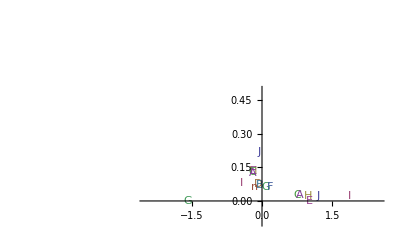

```mathematica
ListPlot[CSummaries,PlotRange->{{-2.5,2.5},{-0.1,0.5}},PlotMarkers->(StringTake[#,-1]&/@CSheets)]
```

#### Oxygen Edge

## Multi-peak fitting with generated data

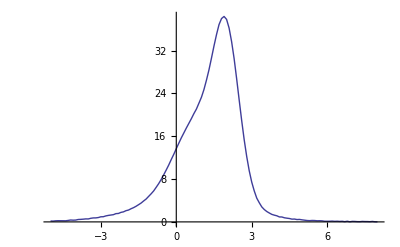

25.1057 ⅇ^(-1.99508 (-1.99902+x)^2)+16.1163 ⅇ^(-0.497021 (-0.990415+x)^2)+3.85703 ⅇ^(-0.116134 (-0.489983+x)^2)

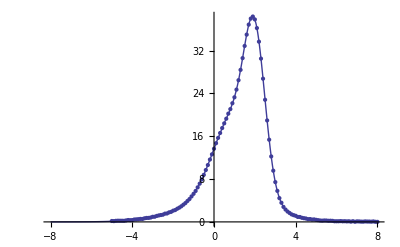

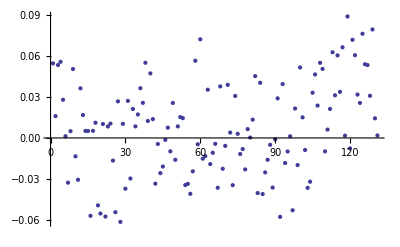

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=Model[data2,3];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

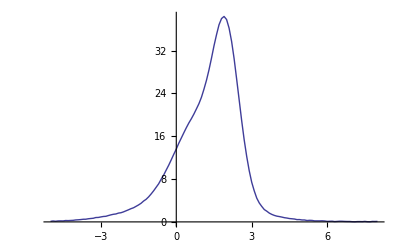

24.9801 ⅇ^(-2.01044 (-1.99924+x)^2)+16.1531 ⅇ^(-0.495882 (-0.99924+x)^2)+3.91041 ⅇ^(-0.118018 (-0.49924+x)^2)

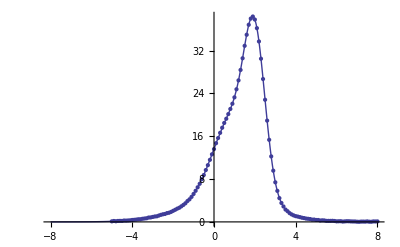

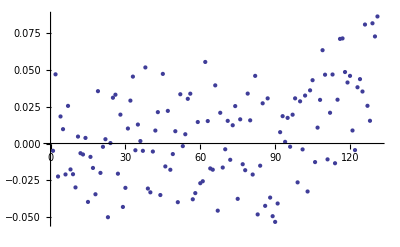

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

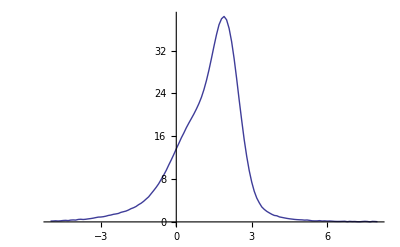

(33.4066 2^(-2.2467 (-1.90903+x)^2))/(1-0.135812 (-1.90903+x)^2)+(1.57346×10^-11 2^(-0.0664325 (-0.909032+x)^2))/(1+0.0354018 (-0.909032+x)^2)+(16.4409 2^(-0.0474042 (-0.409032+x)^2))/(1+1.00537 (-0.409032+x)^2)

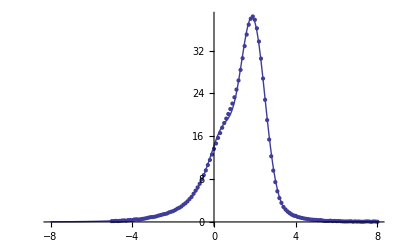

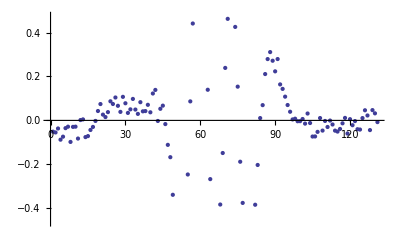

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksVoigtModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```